```mathematica
ClearAll["Global`*"];
ClearAll[crowd,stress];
```

```mathematica
params=<|"u"->1.0,(*baseline inflow/demand driving crowding*)
"mu"->1.0,(*crowd relaxation rate*)
"a"->1.4,(*crowd-stress coupling*)
"b"->1.4      (*stress natural recovery rate*)|>;

{u,mu,a,b}=params/@{"u","mu","a","b"};

(*Simulation horizon*)
t0=0;t1=20;

(*Initial condition*)
C0=0.2;
S0=0.1;

(*Model definition*)
eqs={crowd'[t]==u-mu crowd[t],stress'[t]==a crowd[t]-b stress[t],crowd[t0]==C0,stress[t0]==S0};

(*Vector field for phase portrait and custom solvers*)
f[{c_,s_}]:={u-mu c,a c-b s};

(*Analytical solution*)
solExact=First@DSolve[eqs,{crowd,stress},t];

CExact[t_]:=Evaluate[crowd[t]/. solExact];
SExact[t_]:=Evaluate[stress[t]/. solExact];

(*Exponential convergence (time series)*)
pExactTS=Plot[{CExact[t],SExact[t]},{t,t0,t1},
PlotLegends->Placed[{"C(t) crowding","S(t) stress"},Above],
AxesLabel->{"t","state"},PlotRange->All,ImageSize->Large];
```

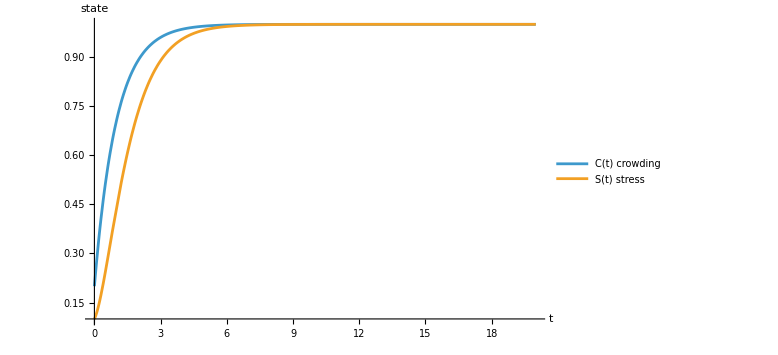

```mathematica
pExactTS
```

```mathematica
fp=Solve[{u-mu c==0,a c-b s==0},{c,s}]//First;
{cStar,sStar}={c,s}/. fp//N;

(*Jacobian of f*)
J=D[f[{c,s}],{{c,s}}]//Simplify;
eig=Eigenvalues[J]//Simplify;

stabilityText=Grid[{{"Fixed point (C*, S*)",{cStar,sStar}},{"Jacobian J",MatrixForm[J]},{"Eigenvalues",eig},{"Classification",If[And@@(Re[#]<0&/@eig),"Stable Node","Not asymptotically stable (check parameters)"]}},Frame->All,Spacings->{2,1}];
```

```mathematica
stabilityText
```

Fixed point (C*, S*) | {1.,1.}
Jacobian J | (-1. | 0
1.4 | -1.4)
Eigenvalues | {-1.4,-1.}
Classification | Stable Node

```mathematica
cNull=u/mu;
sNull[c_]:=(a/b) c;

cMin=Max[0,cStar-1.5];cMax=cStar+2.0;
sMin=Max[0,sStar-1.5];sMax=sStar+2.0;

pStream=StreamPlot[Evaluate[f[{c,s}]],{c,cMin,cMax},{s,sMin,sMax},StreamPoints->Fine,StreamScale->Medium,AxesLabel->{"C","S"},PlotRange->All,ImageSize->Large,PlotLabel->"Phase Portrait (C–S)"];

pNull=Show[pStream,Graphics[{Thick,{Dashed,Line[{{cNull,sMin},{cNull,sMax}}]},{Darker@Gray,Line[{{cMin,sNull[cMin]},{cMax,sNull[cMax]}}]},{Black,PointSize[0.02],Point[{cStar,sStar}]},Inset[Style["(C*,S*)",12],{cStar,sStar},{1,-1}]}],PlotRange->All];
```

```mathematica
icsList={{0.1,0.1},{cMax,sMin+0.2},{cMin+0.2,sMax},{cMax,sMax}};

solTraj=Table[First@NDSolve[{crowd'[t]==u-mu crowd[t],stress'[t]==a crowd[t]-b stress[t],crowd[t0]==ic[[1]],stress[t0]==ic[[2]]},{crowd,stress},{t,t0,t1}],{ic,icsList}];

pTraj=Show[pNull,Table[ParametricPlot[Evaluate[{crowd[t],stress[t]}/. solTraj[[k]]],{t,t0,t1},PlotRange->All],{k,Length[icsList]}],PlotLabel->"Phase Portrait + Nullclines + Trajectories"];
```

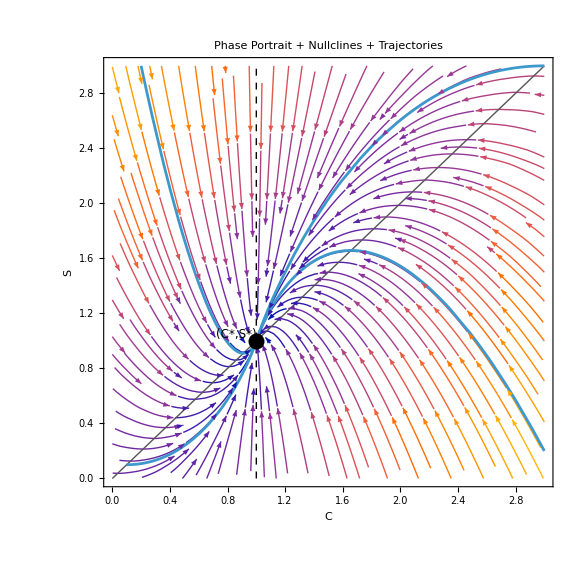

```mathematica
pTraj
```

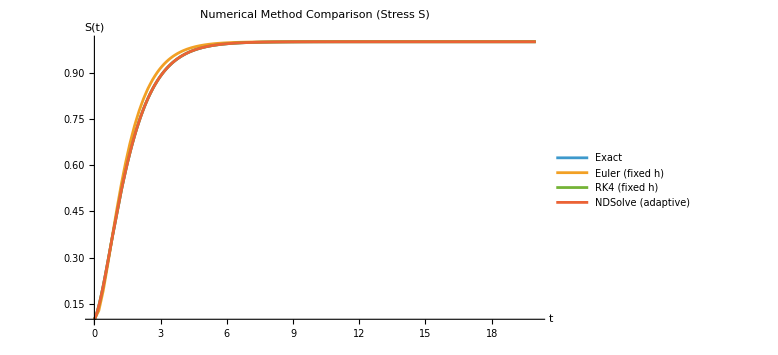

```mathematica
eulerSolve[f_,y0_,{t0_,t1_},h_]:=Module[{n,ts,ys},n=Ceiling[(t1-t0)/h];
ts=t0+Range[0,n]*h;
ys=NestList[#+h f[#]&,y0,n];
Interpolation[Transpose[{ts,ys}],InterpolationOrder->1]];

(*RK4 integrator*)
rk4Solve[f_,y0_,{t0_,t1_},h_]:=Module[{n,ts,step,ys},n=Ceiling[(t1-t0)/h];
ts=t0+Range[0,n]*h;
step[y_]:=Module[{k1,k2,k3,k4},k1=f[y];
k2=f[y+(h/2) k1];
k3=f[y+(h/2) k2];
k4=f[y+h k3];
y+(h/6) (k1+2 k2+2 k3+k4)];
ys=NestList[step,y0,n];
Interpolation[Transpose[{ts,ys}],InterpolationOrder->3]];

yExact[t_]:={CExact[t],SExact[t]};

(*Compare for one representative step size*)
hDemo=0.2;
y0vec={C0,S0};

yEuler=eulerSolve[f,y0vec,{t0,t1},hDemo];
yRK4=rk4Solve[f,y0vec,{t0,t1},hDemo];

(*NDSolve numeric*)
solNDS=First@NDSolve[eqs,{crowd,stress},{t,t0,t1}];
yNDS[t_]:=Evaluate[{crowd[t],stress[t]}/. solNDS];

pCompare=Plot[{yExact[t][[2]],yEuler[t][[2]],yRK4[t][[2]],yNDS[t][[2]]},{t,t0,t1},PlotLegends->Placed[{"Exact","Euler (fixed h)","RK4 (fixed h)","NDSolve (adaptive)"},Above],AxesLabel->{"t","S(t)"},PlotRange->All,ImageSize->Large,PlotLabel->"Numerical Method Comparison (Stress S)"];
pCompare
```

```mathematica
hs={0.8,0.4,0.2,0.1,0.05};

(*sample times for error estimation*)
tsSample=Subdivide[t0,t1,500];

errInfinity[interp_]:=Max[Norm[interp[#]-yExact[#],Infinity]&/@tsSample];

errsEuler=Table[With[{y=eulerSolve[f,y0vec,{t0,t1},h]},{h,errInfinity[y]}],{h,hs}];

errsRK4=Table[With[{y=rk4Solve[f,y0vec,{t0,t1},h]},{h,errInfinity[y]}],{h,hs}];

pErr=ListLogLogPlot[{errsEuler,errsRK4},Joined->True,PlotMarkers->Automatic,AxesLabel->{"step size h","max error (∞-norm)"},PlotLegends->Placed[{"Euler","RK4"},Above],ImageSize->Large,PlotLabel->"Error vs Step Size (Accuracy / Stability Evidence)"];
```

Method | Expected order | Observed order (approx)
Euler | 1 | 1.10
RK4 | 4 | 4.05

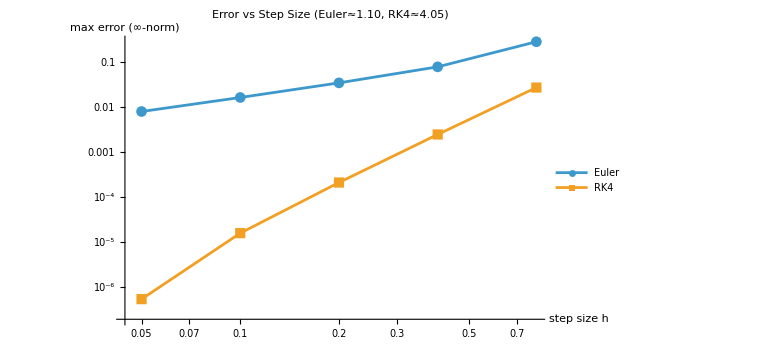

```mathematica
orderEstimate[data_]:=Module[{d,h,e,p},d=Reverse@SortBy[data,First];(*large h to small h*)h=d[[All,1]];
e=d[[All,2]];
p=Log[Most[e]/Rest[e]]/Log[Most[h]/Rest[h]];
Mean[Take[p,-3]]                       (*use last 3 ratios*)];

pEulerObs=orderEstimate[errsEuler];
pRK4Obs=orderEstimate[errsRK4];

orderTable=Grid[{{"Method","Expected order","Observed order (approx)"},{"Euler",1,NumberForm[pEulerObs,{3,2}]},{"RK4",4,NumberForm[pRK4Obs,{3,2}]}},Frame->All,Spacings->{2,1}];

(*Updated error plot*)
pErr2=Show[pErr,PlotLabel->Row[{"Error vs Step Size (Euler≈",NumberForm[pEulerObs,{3,2}],", RK4≈",NumberForm[pRK4Obs,{3,2}],")"}]];
orderTable
pErr2
```

```mathematica
tc=1/mu;   (*crowd recovery time scale*)
ts=1/b;    (*stress recovery time scale*)

timeScales=Grid[{{"Characteristic time (crowding)","t_c = 1/μ",tc},{"Characteristic time (stress)","t_s = 1/b",ts}},Frame->All,Spacings->{2,1}];
```

```mathematica
timeScales
```

Characteristic time (crowding) | t_c = 1/μ | 1.
Characteristic time (stress) | t_s = 1/b | 0.714286